# Coherent states

```mathematica
<<Wolfram`QuantumFramework`

creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[SparseArray[Band[{1,2}]->√Range[n-1],{n,n}],n];
ca=aa["Dagger"];
{aa,ca}]

fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
```

The number states |n⟩ have a uniform phase distribution from 0 to 2π, meaning there is not a defined phase. One may think that the classical limit is when the number of photons of a number state goes to ∞ , but that is not the case because ⟨n| E_x|n⟩  = 0 for any n. We seek states such the expectation of the field operator oscillates sinusoidally , we introduce the coherent states  that are the “most classical” states of the quantum harmonic oscillator.

## Eigenstates of the annihilation operator and minimum uncertainty

If we consider the superposition of number states that differ in ± 1, for example |ψ⟩ = c_n|n⟩ + c_(n+1)|n+1⟩ will have non zero expectation for the electric field operator. More generally, a superposition of all number states will also hold that property, the replacement of â and (â)^† by continuous variables  produces a classical field. A unique way to perform the replacement is to find eigenstates of annihilation operator , in other words solving the eigenvalue equation 
 where α can be in general complex because the operator is not Hermitian.

We can expand |α⟩ in the complete Fock basis 

And replacing in the eigenstate equation and comparing coefficients we can get a recurrence relation C_n √n = α C_(n-1) which is not difficult to solve and  a compact form can be expressed in function of C_0
      C_0 can be found from normalization yielding

Using this we can define a not normalized coherent state in a truncated Fock space, the normalization can be done when needed:
coherentTrunc[ d_]    :=      Not normalized coherent state with complex amplitude α (as QuantumState parameter)  in a Fock space of size d

```mathematica
coherentTrunc[d_]:= QuantumState[FoldList[Function[{prevCoeff,n},(α/Sqrt[n+1]) prevCoeff],1,Range[0,d-2]],d,"Parameters"->α]
```

Right annihilation operator eigenstate(we compare the amplitudes except the last one because we are using a finite basis):

```mathematica
αket =coherentTrunc[20]
```

QuantumState[…]

```mathematica
a = creationAnnihilation[20][[1]];
```

```mathematica
(a[αket]- α αket)["Amplitudes"]//Values //Most
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Analyzing the expected value of the electric field operator:

```mathematica
Ex = ⅈ √((h ω)/(2 Subscript[ϵ, 0] V))(a Exp[ⅈ(Dot[k,r]-ω t)]-a["Dagger"]Exp[-ⅈ(Dot[k,r]-ω t)]);
```

It is the same as  ⅈ √((ℏ ω)/(2 ϵ_0 V))(α ⅇ^(ⅈ (k.r - ω t))-α^*ⅇ^(-ⅈ (k.r - ω t))) resembling a classical field:

```mathematica
αrandom = 2 Exp[ⅈ Exp[RandomReal[{0,2π}]]];
```

```mathematica
With[{state=αket[αrandom]["Normalize"]},(state["Dagger"]@Ex@state)["Scalar"]]//FullSimplify//Chop
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

```mathematica
ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (αrandom Exp[ⅈ (k.r-ω t)]-Conjugate[αrandom] Exp[-ⅈ (k.r-ω t)])//FullSimplify//Chop
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

Or in polar form α = |α| ⅇ^(ⅈ θ), ⟨ α | E_x(r, t) | α ⟩ = 2|α|√((h ω)/(2 ϵ_0 V)) sin(ω t - k. r-θ):

```mathematica
2 Abs[αrandom] √((h ω)/(2V Subscript[ϵ, 0])) Sin[ω t - Dot[k,r]-Arg[αrandom]]//TrigExpand//FullSimplify
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

It can be shown that ⟨ α | (E^2)_x(r, t) | α ⟩ =(h ω)/(2 ϵ_0 V) [1+4|α|^2 sin^2(ω t - k. r-θ)
so Δ E_x = √((h ω)/(2 ϵ_0 V))   is one of the expressions that corresponds to the vacuum fluctuations so the coherent state has field mean classical-like values and mean fluctuations of the vacuum

```mathematica
With[{state=αket[αrandom]["Normalize"]},(state["Dagger"]@Ex@Ex@state)["Scalar"]]//FullSimplify//Chop
```

(h ω (4.5+0.769435 Cos[2 t ω-2 k.r]-3.9253 Sin[2 t ω-2 k.r]))/(V ϵ_0)

```mathematica
√(%-(%%%)^2//FullSimplify //Chop[#,10^-6]&)
```

0.707107 √((h ω)/(V ϵ_0))

Another check is using the quadrature operators  X_i  from section 1.3 , the coherent states  minimize the uncertainty inequality with both quadrature uncertainties being the same. ⟨((ΔX_1))^2⟩_α= ⟨((ΔX_2))^2⟩_α=1/4

```mathematica
X1 := 1/2(a+a["Dagger"]);
X2 := ⅈ/2(a["Dagger"]-a);
```

```mathematica
quantumVariance[ψ_QuantumState,A_QuantumOperator]:= (ψ["Dagger"]@A@A@ψ)["Scalar"]-((ψ["Dagger"]@A@ψ)["Scalar"])^2
```

```mathematica
With[{s =coherentTrunc[20][αrandom]["Normalize"]},quantumVariance[s,#]&/@{X1,X2}]//Chop
```

{0.25,0.25}

The interpretation of α in a phase space context is α = ⟨ X_1⟩ + ⅈ ⟨ X_2⟩ obtained from seeking states that saturate the uncertainty inequality and solving certain eigenvalue equation given that [X_1,X_2] = ⅈ/2
Another physical interpretation of α is related to the photon number operator, it is easy to verify n^— = ⟨ α | n | α ⟩ = | α |^2

```mathematica
coh = coherentTrunc[a["OutputDimension"]]["Normalize"];
```

The random α was chosen a complex number with norm 2, so the expectation returns 4

```mathematica
numberOp = a["Dagger"]@a;
(coh[αrandom]["Dagger"]@numberOp@coh[αrandom])["Scalar"]//Chop
```

4.

Δ n = √(|α|^4+|α|^2-(|α|^2)^2)  = √(n^—)

```mathematica
√quantumVariance[coh[αrandom],numberOp]//Chop
```

2.

This shows that the photon distribution follows a Poisson distribution, this is more clearly shown when calculating P_n the probability of measuring n photons. From the definition of coherent state in Fock basis it is not difficult to obtain P_n = e^(-|a|^2) (|a|^(2 n))/(√(n!)) = e^(- n^—) ((n^—)^n)/(√(n!)) 
The fractional uncertainty Δn/n^— =  1/√(n^—) decreases with increasing mean photon number. The phase distribution for a coherent state |α⟩ (α = |α| ⅇ^(ⅈ θ)) is 
  
For large |α| the Poisson distribution approximates to a Gaussian so a compact approximation can be derived
𝒫(ψ) ≈  √(2 |α|^2/π) exp(- 2 |α|^2(ψ - (θ))^2)

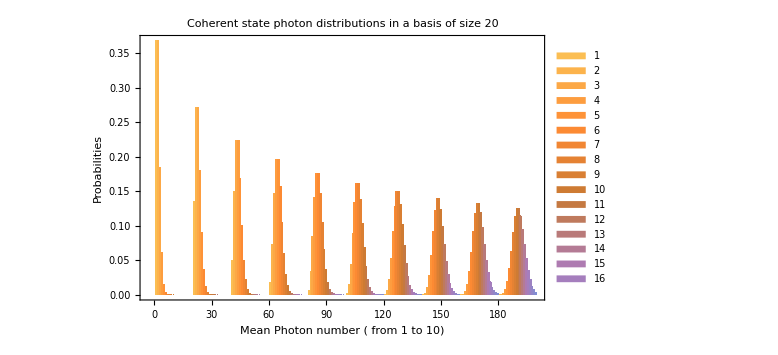

```mathematica
BarChart[Table[coh[√x]["Probabilities"]//Values,{x,1.,10}],]
```

NOTE: Since we are using a truncated basis it is worth noting that to appropriately describe a coherent state with amplitude α, the basis size should be around 
|α |^2+5 |α| (or higher) to include the tails of the  Poisson distribution

For this example |α| = √10the best size would be 10+5 √10 ≈ 25

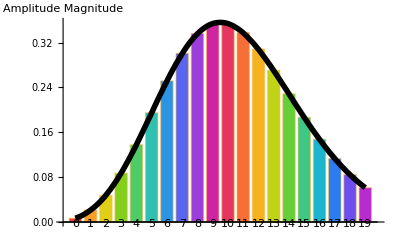

```mathematica
Show[coh[√10 Exp[ⅈ RandomReal[{0,2π}]]]["AmplitudePlot",ChartLegends->Automatic],Out[499],AxesLabel->{"","Amplitude Magnitude"}]
```

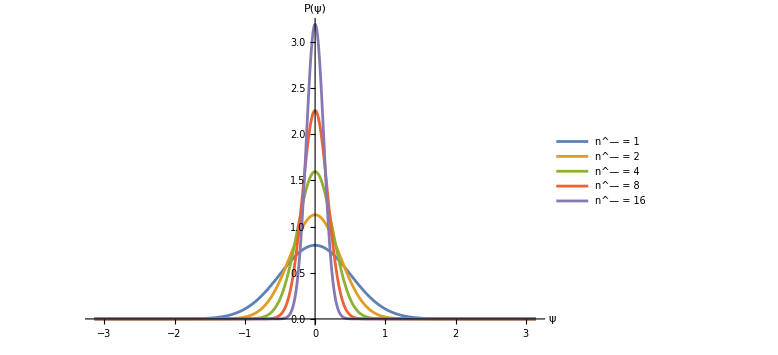

```mathematica
Plot[Evaluate[Table[√((2 Abs[x]^2)/π) Exp[-2 Abs[x]^2 (ψ-Arg[x])^2],{x,{√1,√2,√4,√8,√16}}]],{ψ,-π,π},]
```

So coherent states are quantum states with classical-like  features because:

Mean value of electric field has the form of a classical expression

Electric field fluctuations are those of the vacuum

Fluctuations in the photon number decrease when the mean photon number increases

Their phase becomes more localized when the mean photon number increases

## Displacement operator and displaced vacuum states

There exists an additional equivalent definition of a coherent state that is based on displacing the vacuum state , that can give more insight why coherent states have must have the uncertainty of the vacuum. The generator is the displacement operator that also has some nice algebraic properties, it is defined as:

and a coherent state can be build as

Using the disentangling theorem e^(Â + B̂) = e^(Â) e^(B̂) e^(-1/2 [A, B]) valid when [A, B] ≠ 0 but [A, [A, B]] = [B, [A, B] ] = 0 holds
⇒ D(α) = e^(-1/2 |α|^2)e^(α a^†)e^(- α^*a) so applying to vacuum
Expanding  e^(-α^*a) |0⟩ = ∑_k ((-α^*a)^k)/(k!) |0⟩ = |0⟩ because the annihilation operator and their powers kill the vacuum state except when k = 0
e^(α a^†) |0⟩ = ∑_(n=0)^∞ ((α a^†)^n)/(n!)|0⟩ = ∑_(n=0)^∞  α^n/(√(n!))|n⟩, because (a^†)^n |0⟩ = √(n!) |n⟩ so D(α) |0⟩ is exactly the same as the previous definition

Defining the displacement operator ( we will just work numerically because symbolically this definition can have really slow execution times):

```mathematica
Clear[disp]
disp[α_?NumberQ]:= Exp[α a["Dagger"]-α* a]
```

```mathematica
(disp[αrandom][]-coh[αrandom])["Amplitudes"]//Values
```

{-6.90244×10^-10,8.77259×10^-10+1.06591×10^-9 ⅈ,3.75542×10^-10-1.91585×10^-9 ⅈ,-1.98369×10^-9+1.07098×10^-9 ⅈ,2.08753×10^-9+8.51094×10^-10 ⅈ,-5.98666×10^-10-1.92519×10^-9 ⅈ,-9.03978×10^-10+1.37767×10^-9 ⅈ,1.22857×10^-9-1.33105×10^-10 ⅈ,-6.63582×10^-10-6.48964×10^-10 ⅈ,0.+3.4313×10^-10 ⅈ,1.2277×10^-9-8.45279×10^-10 ⅈ,4.37303×10^-9+1.25375×10^-9 ⅈ,7.55098×10^-9+1.74017×10^-8 ⅈ,-3.14091×10^-8+6.14101×10^-8 ⅈ,-2.30088×10^-7+5.04477×10^-8 ⅈ,-5.88887×10^-7-4.63052×10^-7 ⅈ,-4.95859×10^-8-2.22585×10^-6 ⅈ,4.69225×10^-6-4.04039×10^-6 ⅈ,0.0000159069+2.75169×10^-6 ⅈ,0.0000195429+0.0000343453 ⅈ}

Using a truncated basis has additional numeric error propagation because [a, a^†] is not exactly the identity. Using a bigger space size or reducing the magnitude of α can control the desired precision.

```mathematica
a = creationAnnihilation[35][[1]];
coh = coherentTrunc[35]["Normalize"];
```

```mathematica
(disp[αrandom][]-coh[αrandom])["Amplitudes"]//Values
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
αrandom = RandomComplex[{0,3+3I}];
```

D^†(α) = D (-α)

```mathematica
((disp[αrandom]["Dagger"]["Matrix"] - disp[-αrandom]["Matrix"])//Chop )["NonzeroPositions"]
```

{}

It is clear D^†(α) D(α) = D(α) D^†(α) = 1 , is a unitary operator

```mathematica
disp[αrandom]["UnitaryQ"]
```

True

Composing two displacement operators also has the form of a displacement operator times an overall phase factor 
 D(α) D(β) = e^(ⅈ Im( α β^*)) D(α + β) (can be proved with disentangling theorem)
 Intuitively if we do a displacement of α and then a displacement of β, the net displacement is α + β
  D(α) D(β) |0⟩ = D(α) |β⟩ = exp(ⅈ Im(α β*)) |α+β⟩

```mathematica
{αrandom,βrandom}= RandomComplex[{-2-2I,2+2I},2]
```

{-1.6409+1.57331 ⅈ,-0.533801+0.490973 ⅈ}

We consider a bigger size because are composing displacements:

```mathematica
a = creationAnnihilation[50][[1]];
coh = coherentTrunc[50]["Normalize"];
```

“AmplitudeList” returns non zero amplitudes, in this case all are zero so the states are the numerically the same

```mathematica
((disp[αrandom]@disp[βrandom][])-Exp[ⅈ Im[αrandom βrandom*]]coh[αrandom + βrandom]//Chop)["AmplitudeList"]
```

{}

## Wave packets and time evolution

```mathematica
{a,a†} = creationAnnihilation[20];
```

The position operator q̂ is defined, such that q̂ |q⟩ = q |q⟩ describes the position eigenstates:

```mathematica
q = √(h/(2m ω))X1;
```

The Fock states wave functions are the following (derivations can be found in standard quantum mechanics textbooks regarding a quantum harmonic oscillator):
  where ξ = q √(m ω/h)  and H_n are Hermite polynomials

Then the wave function for a coherent state is:

It can be simplified and it takes the form of a gaussian, and the probability distribution |ψ_α(q)|^2 also takes the form of a gaussian

```mathematica
((m ω)/(π h))^(1/4)ⅇ^(-Abs[α]^2/2)ⅇ^(-ξ^2/2)ⅇ^(ξ^2)FullSimplify[(ⅇ^(-ξ^2) Sum[(z)^n/n!HermiteH[n,ξ],{n,0,∞}])]/.z->α/√2
```

(ⅇ^(-(α/(√2)-ξ)^2+ξ^2/2-Abs[α]^2/2) ((m ω)/h)^(1/4))/π^(1/4)

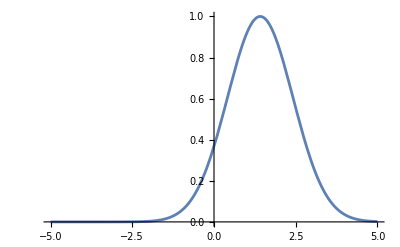

```mathematica
Plot[%[[1]] /. α->1,{ξ,-5,5}]
```

The diagonal quantum harmonic oscillator Hamiltonian for a single mode field:

```mathematica
H = h ω (a†@a +1/2 QuantumOperator["I"[a["OutputDimension"]]]);
```

```mathematica
H["Formula"]
```

(h ω)/2 00+(3 h ω)/2 11+(5 h ω)/2 22+(7 h ω)/2 33+(9 h ω)/2 44+(11 h ω)/2 55+(13 h ω)/2 66+(15 h ω)/2 77+(17 h ω)/2 88+(19 h ω)/2 99+(21 h ω)/2 1010+(23 h ω)/2 1111+(25 h ω)/2 1212+(27 h ω)/2 1313+(29 h ω)/2 1414+(31 h ω)/2 1515+(33 h ω)/2 1616+(35 h ω)/2 1717+(37 h ω)/2 1818+(39 h ω)/2 1919

We create an evolution operator to evolve the states at any time:

```mathematica
QOE=QuantumOperator[QuantumEvolve[H/h,None,t],"Parameters"->t];
```

A coherent state  remains a coherent state under the evolution but the complex amplitude phase depends on time, with an extra global phase 
| ψ(t) ⟩ = ⅇ^(- ⅈ ω t / 2) |α ⅇ^(-ⅈ ω t)⟩

```mathematica
symbolicCoh = coherentTrunc[a["Dimensions"][[1]]];
```

```mathematica
(QOE @ symbolicCoh) == ⅇ^(-ⅈ ω t/2)symbolicCoh[α ⅇ^(-ⅈ ω t)]
```

True

The mean value of the position operator for the evolved state, behaves like it was a classical oscillator (sinusoidal oscillations). This emphasises why coherent states are called “the most classical” quantum states. This also holds for the mean value of the momentum operator.

```mathematica
αc = RandomComplex[√2{-1-ⅈ,1+ⅈ}]
```

0.638275+1.40609 ⅈ

```mathematica
states=Table[{t,QOE[t][coh[αc]]},{t,0,10,0.25}];
```

{7.61275,Null}

```mathematica
meanPosition=MapAt[((#["Dagger"]@q@#)["Scalar"]&),#,2]& /@ states ;
```

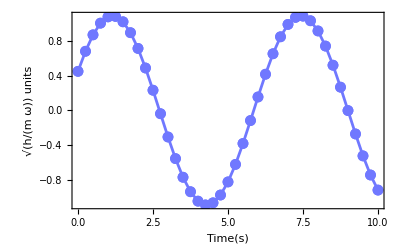

```mathematica
ListLinePlot[Re[meanPosition/.{h->1,m->1,ω->1}],]
```

## More properties of coherent states

The  inner  product   of  two  coherent  states | α⟩,  | β ⟩

```mathematica
{αc,βc} = RandomComplex[{1.5+1.5I},2]
```

{0.706839+1.1843 ⅈ,1.07218+0.896704 ⅈ}

```mathematica
(coh[αc]["Dagger"]@coh[βc])["Scalar"]
```

0.722082-0.533091 ⅈ

```mathematica
Exp[1/2(βc*αc-βc αc*)]Exp[-1/2 Abs[βc-αc]^2]
```

0.722082+0.533091 ⅈ

```mathematica
{αc,βc} = {2.9,1.}
```

{2.9,1.}

```mathematica
(coh[αc]["Dagger"]@coh[βc])["Scalar"]
```

0.164513

```mathematica
coherentTrunc[20]@coherentTrunc[20]["Dagger"]
```

$Aborted

```mathematica
QuantumOperator[coherentTrunc[20]@coherentTrunc[20]["Dagger"],20]
```

00+Conjugate[α]01+Conjugate[α]^2/(√2)02+Conjugate[α]^3/(√6)03+Conjugate[α]^4/(2 √6)04+Conjugate[α]^5/(2 √30)05+Conjugate[α]^6/(12 √5)06+Conjugate[α]^7/(12 √35)07+Conjugate[α]^8/(24 √70)08+Conjugate[α]^9/(72 √70)09+Conjugate[α]^10/(720 √7)010+Conjugate[α]^11/(720 √77)011+Conjugate[α]^12/(1440 √231)012+Conjugate[α]^13/(1440 √3003)013+Conjugate[α]^14/(10080 √858)014+Conjugate[α]^15/(30240 √1430)015+Conjugate[α]^16/(120960 √1430)016+Conjugate[α]^17/(120960 √24310)017+Conjugate[α]^18/(725760 √12155)018+Conjugate[α]^19/(725760 √230945)019+α10+α Conjugate[α]11+(α Conjugate[α]^2)/(√2)12+(α Conjugate[α]^3)/(√6)13+(α Conjugate[α]^4)/(2 √6)14+(α Conjugate[α]^5)/(2 √30)15+(α Conjugate[α]^6)/(12 √5)16+(α Conjugate[α]^7)/(12 √35)17+(α Conjugate[α]^8)/(24 √70)18+(α Conjugate[α]^9)/(72 √70)19+(α Conjugate[α]^10)/(720 √7)110+(α Conjugate[α]^11)/(720 √77)111+(α Conjugate[α]^12)/(1440 √231)112+(α Conjugate[α]^13)/(1440 √3003)113+(α Conjugate[α]^14)/(10080 √858)114+(α Conjugate[α]^15)/(30240 √1430)115+(α Conjugate[α]^16)/(120960 √1430)116+(α Conjugate[α]^17)/(120960 √24310)117+(α Conjugate[α]^18)/(725760 √12155)118+(α Conjugate[α]^19)/(725760 √230945)119+α^2/(√2)20+(α^2 Conjugate[α])/(√2)21+1/2 α^2 Conjugate[α]^222+(α^2 Conjugate[α]^3)/(2 √3)23+(α^2 Conjugate[α]^4)/(4 √3)24+(α^2 Conjugate[α]^5)/(4 √15)25+(α^2 Conjugate[α]^6)/(12 √10)26+(α^2 Conjugate[α]^7)/(12 √70)27+(α^2 Conjugate[α]^8)/(48 √35)28+(α^2 Conjugate[α]^9)/(144 √35)29+(α^2 Conjugate[α]^10)/(720 √14)210+(α^2 Conjugate[α]^11)/(720 √154)211+(α^2 Conjugate[α]^12)/(1440 √462)212+(α^2 Conjugate[α]^13)/(1440 √6006)213+(α^2 Conjugate[α]^14)/(20160 √429)214+(α^2 Conjugate[α]^15)/(60480 √715)215+(α^2 Conjugate[α]^16)/(241920 √715)216+(α^2 Conjugate[α]^17)/(241920 √12155)217+(α^2 Conjugate[α]^18)/(725760 √24310)218+(α^2 Conjugate[α]^19)/(725760 √461890)219+α^3/(√6)30+(α^3 Conjugate[α])/(√6)31+(α^3 Conjugate[α]^2)/(2 √3)32+1/6 α^3 Conjugate[α]^333+1/12 α^3 Conjugate[α]^434+(α^3 Conjugate[α]^5)/(12 √5)35+(α^3 Conjugate[α]^6)/(12 √30)36+(α^3 Conjugate[α]^7)/(12 √210)37+(α^3 Conjugate[α]^8)/(48 √105)38+(α^3 Conjugate[α]^9)/(144 √105)39+(α^3 Conjugate[α]^10)/(720 √42)310+(α^3 Conjugate[α]^11)/(720 √462)311+(α^3 Conjugate[α]^12)/(4320 √154)312+(α^3 Conjugate[α]^13)/(4320 √2002)313+(α^3 Conjugate[α]^14)/(60480 √143)314+(α^3 Conjugate[α]^15)/(60480 √2145)315+(α^3 Conjugate[α]^16)/(241920 √2145)316+(α^3 Conjugate[α]^17)/(241920 √36465)317+(α^3 Conjugate[α]^18)/(725760 √72930)318+(α^3 Conjugate[α]^19)/(725760 √1385670)319+α^4/(2 √6)40+(α^4 Conjugate[α])/(2 √6)41+(α^4 Conjugate[α]^2)/(4 √3)42+1/12 α^4 Conjugate[α]^343+1/24 α^4 Conjugate[α]^444+(α^4 Conjugate[α]^5)/(24 √5)45+(α^4 Conjugate[α]^6)/(24 √30)46+(α^4 Conjugate[α]^7)/(24 √210)47+(α^4 Conjugate[α]^8)/(96 √105)48+(α^4 Conjugate[α]^9)/(288 √105)49+(α^4 Conjugate[α]^10)/(1440 √42)410+(α^4 Conjugate[α]^11)/(1440 √462)411+(α^4 Conjugate[α]^12)/(8640 √154)412+(α^4 Conjugate[α]^13)/(8640 √2002)413+(α^4 Conjugate[α]^14)/(120960 √143)414+(α^4 Conjugate[α]^15)/(120960 √2145)415+(α^4 Conjugate[α]^16)/(483840 √2145)416+(α^4 Conjugate[α]^17)/(483840 √36465)417+(α^4 Conjugate[α]^18)/(1451520 √72930)418+(α^4 Conjugate[α]^19)/(1451520 √1385670)419+α^5/(2 √30)50+(α^5 Conjugate[α])/(2 √30)51+(α^5 Conjugate[α]^2)/(4 √15)52+(α^5 Conjugate[α]^3)/(12 √5)53+(α^5 Conjugate[α]^4)/(24 √5)54+1/120 α^5 Conjugate[α]^555+(α^5 Conjugate[α]^6)/(120 √6)56+(α^5 Conjugate[α]^7)/(120 √42)57+(α^5 Conjugate[α]^8)/(480 √21)58+(α^5 Conjugate[α]^9)/(1440 √21)59+(α^5 Conjugate[α]^10)/(1440 √210)510+(α^5 Conjugate[α]^11)/(1440 √2310)511+(α^5 Conjugate[α]^12)/(8640 √770)512+(α^5 Conjugate[α]^13)/(8640 √10010)513+(α^5 Conjugate[α]^14)/(120960 √715)514+(α^5 Conjugate[α]^15)/(604800 √429)515+(α^5 Conjugate[α]^16)/(2419200 √429)516+(α^5 Conjugate[α]^17)/(2419200 √7293)517+(α^5 Conjugate[α]^18)/(7257600 √14586)518+(α^5 Conjugate[α]^19)/(7257600 √277134)519+α^6/(12 √5)60+(α^6 Conjugate[α])/(12 √5)61+(α^6 Conjugate[α]^2)/(12 √10)62+(α^6 Conjugate[α]^3)/(12 √30)63+(α^6 Conjugate[α]^4)/(24 √30)64+(α^6 Conjugate[α]^5)/(120 √6)65+1/720 α^6 Conjugate[α]^666+(α^6 Conjugate[α]^7)/(720 √7)67+(α^6 Conjugate[α]^8)/(1440 √14)68+(α^6 Conjugate[α]^9)/(4320 √14)69+(α^6 Conjugate[α]^10)/(8640 √35)610+(α^6 Conjugate[α]^11)/(8640 √385)611+(α^6 Conjugate[α]^12)/(17280 √1155)612+(α^6 Conjugate[α]^13)/(17280 √15015)613+(α^6 Conjugate[α]^14)/(120960 √4290)614+(α^6 Conjugate[α]^15)/(1814400 √286)615+(α^6 Conjugate[α]^16)/(7257600 √286)616+(α^6 Conjugate[α]^17)/(7257600 √4862)617+(α^6 Conjugate[α]^18)/(43545600 √2431)618+(α^6 Conjugate[α]^19)/(43545600 √46189)619+α^7/(12 √35)70+(α^7 Conjugate[α])/(12 √35)71+(α^7 Conjugate[α]^2)/(12 √70)72+(α^7 Conjugate[α]^3)/(12 √210)73+(α^7 Conjugate[α]^4)/(24 √210)74+(α^7 Conjugate[α]^5)/(120 √42)75+(α^7 Conjugate[α]^6)/(720 √7)76+(α^7 Conjugate[α]^7)/5040 77+(α^7 Conjugate[α]^8)/(10080 √2)78+(α^7 Conjugate[α]^9)/(30240 √2)79+(α^7 Conjugate[α]^10)/(60480 √5)710+(α^7 Conjugate[α]^11)/(60480 √55)711+(α^7 Conjugate[α]^12)/(120960 √165)712+(α^7 Conjugate[α]^13)/(120960 √2145)713+(α^7 Conjugate[α]^14)/(120960 √30030)714+(α^7 Conjugate[α]^15)/(1814400 √2002)715+(α^7 Conjugate[α]^16)/(7257600 √2002)716+(α^7 Conjugate[α]^17)/(7257600 √34034)717+(α^7 Conjugate[α]^18)/(43545600 √17017)718+(α^7 Conjugate[α]^19)/(43545600 √323323)719+α^8/(24 √70)80+(α^8 Conjugate[α])/(24 √70)81+(α^8 Conjugate[α]^2)/(48 √35)82+(α^8 Conjugate[α]^3)/(48 √105)83+(α^8 Conjugate[α]^4)/(96 √105)84+(α^8 Conjugate[α]^5)/(480 √21)85+(α^8 Conjugate[α]^6)/(1440 √14)86+(α^8 Conjugate[α]^7)/(10080 √2)87+(α^8 Conjugate[α]^8)/40320 88+(α^8 Conjugate[α]^9)/120960 89+(α^8 Conjugate[α]^10)/(120960 √10)810+(α^8 Conjugate[α]^11)/(120960 √110)811+(α^8 Conjugate[α]^12)/(241920 √330)812+(α^8 Conjugate[α]^13)/(241920 √4290)813+(α^8 Conjugate[α]^14)/(483840 √15015)814+(α^8 Conjugate[α]^15)/(7257600 √1001)815+(α^8 Conjugate[α]^16)/(29030400 √1001)816+(α^8 Conjugate[α]^17)/(29030400 √17017)817+(α^8 Conjugate[α]^18)/(87091200 √34034)818+(α^8 Conjugate[α]^19)/(87091200 √646646)819+α^9/(72 √70)90+(α^9 Conjugate[α])/(72 √70)91+(α^9 Conjugate[α]^2)/(144 √35)92+(α^9 Conjugate[α]^3)/(144 √105)93+(α^9 Conjugate[α]^4)/(288 √105)94+(α^9 Conjugate[α]^5)/(1440 √21)95+(α^9 Conjugate[α]^6)/(4320 √14)96+(α^9 Conjugate[α]^7)/(30240 √2)97+(α^9 Conjugate[α]^8)/120960 98+(α^9 Conjugate[α]^9)/362880 99+(α^9 Conjugate[α]^10)/(362880 √10)910+(α^9 Conjugate[α]^11)/(362880 √110)911+(α^9 Conjugate[α]^12)/(725760 √330)912+(α^9 Conjugate[α]^13)/(725760 √4290)913+(α^9 Conjugate[α]^14)/(1451520 √15015)914+(α^9 Conjugate[α]^15)/(21772800 √1001)915+(α^9 Conjugate[α]^16)/(87091200 √1001)916+(α^9 Conjugate[α]^17)/(87091200 √17017)917+(α^9 Conjugate[α]^18)/(261273600 √34034)918+(α^9 Conjugate[α]^19)/(261273600 √646646)919+α^10/(720 √7)100+(α^10 Conjugate[α])/(720 √7)101+(α^10 Conjugate[α]^2)/(720 √14)102+(α^10 Conjugate[α]^3)/(720 √42)103+(α^10 Conjugate[α]^4)/(1440 √42)104+(α^10 Conjugate[α]^5)/(1440 √210)105+(α^10 Conjugate[α]^6)/(8640 √35)106+(α^10 Conjugate[α]^7)/(60480 √5)107+(α^10 Conjugate[α]^8)/(120960 √10)108+(α^10 Conjugate[α]^9)/(362880 √10)109+(α^10 Conjugate[α]^10)/3628800 1010+(α^10 Conjugate[α]^11)/(3628800 √11)1011+(α^10 Conjugate[α]^12)/(7257600 √33)1012+(α^10 Conjugate[α]^13)/(7257600 √429)1013+(α^10 Conjugate[α]^14)/(7257600 √6006)1014+(α^10 Conjugate[α]^15)/(21772800 √10010)1015+(α^10 Conjugate[α]^16)/(87091200 √10010)1016+(α^10 Conjugate[α]^17)/(87091200 √170170)1017+(α^10 Conjugate[α]^18)/(522547200 √85085)1018+(α^10 Conjugate[α]^19)/(522547200 √1616615)1019+α^11/(720 √77)110+(α^11 Conjugate[α])/(720 √77)111+(α^11 Conjugate[α]^2)/(720 √154)112+(α^11 Conjugate[α]^3)/(720 √462)113+(α^11 Conjugate[α]^4)/(1440 √462)114+(α^11 Conjugate[α]^5)/(1440 √2310)115+(α^11 Conjugate[α]^6)/(8640 √385)116+(α^11 Conjugate[α]^7)/(60480 √55)117+(α^11 Conjugate[α]^8)/(120960 √110)118+(α^11 Conjugate[α]^9)/(362880 √110)119+(α^11 Conjugate[α]^10)/(3628800 √11)1110+(α^11 Conjugate[α]^11)/39916800 1111+(α^11 Conjugate[α]^12)/(79833600 √3)1112+(α^11 Conjugate[α]^13)/(79833600 √39)1113+(α^11 Conjugate[α]^14)/(79833600 √546)1114+(α^11 Conjugate[α]^15)/(239500800 √910)1115+(α^11 Conjugate[α]^16)/(958003200 √910)1116+(α^11 Conjugate[α]^17)/(958003200 √15470)1117+(α^11 Conjugate[α]^18)/(5748019200 √7735)1118+(α^11 Conjugate[α]^19)/(5748019200 √146965)1119+α^12/(1440 √231)120+(α^12 Conjugate[α])/(1440 √231)121+(α^12 Conjugate[α]^2)/(1440 √462)122+(α^12 Conjugate[α]^3)/(4320 √154)123+(α^12 Conjugate[α]^4)/(8640 √154)124+(α^12 Conjugate[α]^5)/(8640 √770)125+(α^12 Conjugate[α]^6)/(17280 √1155)126+(α^12 Conjugate[α]^7)/(120960 √165)127+(α^12 Conjugate[α]^8)/(241920 √330)128+(α^12 Conjugate[α]^9)/(725760 √330)129+(α^12 Conjugate[α]^10)/(7257600 √33)1210+(α^12 Conjugate[α]^11)/(79833600 √3)1211+(α^12 Conjugate[α]^12)/479001600 1212+(α^12 Conjugate[α]^13)/(479001600 √13)1213+(α^12 Conjugate[α]^14)/(479001600 √182)1214+(α^12 Conjugate[α]^15)/(479001600 √2730)1215+(α^12 Conjugate[α]^16)/(1916006400 √2730)1216+(α^12 Conjugate[α]^17)/(1916006400 √46410)1217+(α^12 Conjugate[α]^18)/(11496038400 √23205)1218+(α^12 Conjugate[α]^19)/(11496038400 √440895)1219+α^13/(1440 √3003)130+(α^13 Conjugate[α])/(1440 √3003)131+(α^13 Conjugate[α]^2)/(1440 √6006)132+(α^13 Conjugate[α]^3)/(4320 √2002)133+(α^13 Conjugate[α]^4)/(8640 √2002)134+(α^13 Conjugate[α]^5)/(8640 √10010)135+(α^13 Conjugate[α]^6)/(17280 √15015)136+(α^13 Conjugate[α]^7)/(120960 √2145)137+(α^13 Conjugate[α]^8)/(241920 √4290)138+(α^13 Conjugate[α]^9)/(725760 √4290)139+(α^13 Conjugate[α]^10)/(7257600 √429)1310+(α^13 Conjugate[α]^11)/(79833600 √39)1311+(α^13 Conjugate[α]^12)/(479001600 √13)1312+(α^13 Conjugate[α]^13)/6227020800 1313+(α^13 Conjugate[α]^14)/(6227020800 √14)1314+(α^13 Conjugate[α]^15)/(6227020800 √210)1315+(α^13 Conjugate[α]^16)/(24908083200 √210)1316+(α^13 Conjugate[α]^17)/(24908083200 √3570)1317+(α^13 Conjugate[α]^18)/(149448499200 √1785)1318+(α^13 Conjugate[α]^19)/(149448499200 √33915)1319+α^14/(10080 √858)140+(α^14 Conjugate[α])/(10080 √858)141+(α^14 Conjugate[α]^2)/(20160 √429)142+(α^14 Conjugate[α]^3)/(60480 √143)143+(α^14 Conjugate[α]^4)/(120960 √143)144+(α^14 Conjugate[α]^5)/(120960 √715)145+(α^14 Conjugate[α]^6)/(120960 √4290)146+(α^14 Conjugate[α]^7)/(120960 √30030)147+(α^14 Conjugate[α]^8)/(483840 √15015)148+(α^14 Conjugate[α]^9)/(1451520 √15015)149+(α^14 Conjugate[α]^10)/(7257600 √6006)1410+(α^14 Conjugate[α]^11)/(79833600 √546)1411+(α^14 Conjugate[α]^12)/(479001600 √182)1412+(α^14 Conjugate[α]^13)/(6227020800 √14)1413+(α^14 Conjugate[α]^14)/87178291200 1414+(α^14 Conjugate[α]^15)/(87178291200 √15)1415+(α^14 Conjugate[α]^16)/(348713164800 √15)1416+(α^14 Conjugate[α]^17)/(348713164800 √255)1417+(α^14 Conjugate[α]^18)/(1046139494400 √510)1418+(α^14 Conjugate[α]^19)/(1046139494400 √9690)1419+α^15/(30240 √1430)150+(α^15 Conjugate[α])/(30240 √1430)151+(α^15 Conjugate[α]^2)/(60480 √715)152+(α^15 Conjugate[α]^3)/(60480 √2145)153+(α^15 Conjugate[α]^4)/(120960 √2145)154+(α^15 Conjugate[α]^5)/(604800 √429)155+(α^15 Conjugate[α]^6)/(1814400 √286)156+(α^15 Conjugate[α]^7)/(1814400 √2002)157+(α^15 Conjugate[α]^8)/(7257600 √1001)158+(α^15 Conjugate[α]^9)/(21772800 √1001)159+(α^15 Conjugate[α]^10)/(21772800 √10010)1510+(α^15 Conjugate[α]^11)/(239500800 √910)1511+(α^15 Conjugate[α]^12)/(479001600 √2730)1512+(α^15 Conjugate[α]^13)/(6227020800 √210)1513+(α^15 Conjugate[α]^14)/(87178291200 √15)1514+(α^15 Conjugate[α]^15)/1307674368000 1515+(α^15 Conjugate[α]^16)/5230697472000 1516+(α^15 Conjugate[α]^17)/(5230697472000 √17)1517+(α^15 Conjugate[α]^18)/(15692092416000 √34)1518+(α^15 Conjugate[α]^19)/(15692092416000 √646)1519+α^16/(120960 √1430)160+(α^16 Conjugate[α])/(120960 √1430)161+(α^16 Conjugate[α]^2)/(241920 √715)162+(α^16 Conjugate[α]^3)/(241920 √2145)163+(α^16 Conjugate[α]^4)/(483840 √2145)164+(α^16 Conjugate[α]^5)/(2419200 √429)165+(α^16 Conjugate[α]^6)/(7257600 √286)166+(α^16 Conjugate[α]^7)/(7257600 √2002)167+(α^16 Conjugate[α]^8)/(29030400 √1001)168+(α^16 Conjugate[α]^9)/(87091200 √1001)169+(α^16 Conjugate[α]^10)/(87091200 √10010)1610+(α^16 Conjugate[α]^11)/(958003200 √910)1611+(α^16 Conjugate[α]^12)/(1916006400 √2730)1612+(α^16 Conjugate[α]^13)/(24908083200 √210)1613+(α^16 Conjugate[α]^14)/(348713164800 √15)1614+(α^16 Conjugate[α]^15)/5230697472000 1615+(α^16 Conjugate[α]^16)/20922789888000 1616+(α^16 Conjugate[α]^17)/(20922789888000 √17)1617+(α^16 Conjugate[α]^18)/(62768369664000 √34)1618+(α^16 Conjugate[α]^19)/(62768369664000 √646)1619+α^17/(120960 √24310)170+(α^17 Conjugate[α])/(120960 √24310)171+(α^17 Conjugate[α]^2)/(241920 √12155)172+(α^17 Conjugate[α]^3)/(241920 √36465)173+(α^17 Conjugate[α]^4)/(483840 √36465)174+(α^17 Conjugate[α]^5)/(2419200 √7293)175+(α^17 Conjugate[α]^6)/(7257600 √4862)176+(α^17 Conjugate[α]^7)/(7257600 √34034)177+(α^17 Conjugate[α]^8)/(29030400 √17017)178+(α^17 Conjugate[α]^9)/(87091200 √17017)179+(α^17 Conjugate[α]^10)/(87091200 √170170)1710+(α^17 Conjugate[α]^11)/(958003200 √15470)1711+(α^17 Conjugate[α]^12)/(1916006400 √46410)1712+(α^17 Conjugate[α]^13)/(24908083200 √3570)1713+(α^17 Conjugate[α]^14)/(348713164800 √255)1714+(α^17 Conjugate[α]^15)/(5230697472000 √17)1715+(α^17 Conjugate[α]^16)/(20922789888000 √17)1716+(α^17 Conjugate[α]^17)/355687428096000 1717+(α^17 Conjugate[α]^18)/(1067062284288000 √2)1718+(α^17 Conjugate[α]^19)/(1067062284288000 √38)1719+α^18/(725760 √12155)180+(α^18 Conjugate[α])/(725760 √12155)181+(α^18 Conjugate[α]^2)/(725760 √24310)182+(α^18 Conjugate[α]^3)/(725760 √72930)183+(α^18 Conjugate[α]^4)/(1451520 √72930)184+(α^18 Conjugate[α]^5)/(7257600 √14586)185+(α^18 Conjugate[α]^6)/(43545600 √2431)186+(α^18 Conjugate[α]^7)/(43545600 √17017)187+(α^18 Conjugate[α]^8)/(87091200 √34034)188+(α^18 Conjugate[α]^9)/(261273600 √34034)189+(α^18 Conjugate[α]^10)/(522547200 √85085)1810+(α^18 Conjugate[α]^11)/(5748019200 √7735)1811+(α^18 Conjugate[α]^12)/(11496038400 √23205)1812+(α^18 Conjugate[α]^13)/(149448499200 √1785)1813+(α^18 Conjugate[α]^14)/(1046139494400 √510)1814+(α^18 Conjugate[α]^15)/(15692092416000 √34)1815+(α^18 Conjugate[α]^16)/(62768369664000 √34)1816+(α^18 Conjugate[α]^17)/(1067062284288000 √2)1817+(α^18 Conjugate[α]^18)/6402373705728000 1818+(α^18 Conjugate[α]^19)/(6402373705728000 √19)1819+α^19/(725760 √230945)190+(α^19 Conjugate[α])/(725760 √230945)191+(α^19 Conjugate[α]^2)/(725760 √461890)192+(α^19 Conjugate[α]^3)/(725760 √1385670)193+(α^19 Conjugate[α]^4)/(1451520 √1385670)194+(α^19 Conjugate[α]^5)/(7257600 √277134)195+(α^19 Conjugate[α]^6)/(43545600 √46189)196+(α^19 Conjugate[α]^7)/(43545600 √323323)197+(α^19 Conjugate[α]^8)/(87091200 √646646)198+(α^19 Conjugate[α]^9)/(261273600 √646646)199+(α^19 Conjugate[α]^10)/(522547200 √1616615)1910+(α^19 Conjugate[α]^11)/(5748019200 √146965)1911+(α^19 Conjugate[α]^12)/(11496038400 √440895)1912+(α^19 Conjugate[α]^13)/(149448499200 √33915)1913+(α^19 Conjugate[α]^14)/(1046139494400 √9690)1914+(α^19 Conjugate[α]^15)/(15692092416000 √646)1915+(α^19 Conjugate[α]^16)/(62768369664000 √646)1916+(α^19 Conjugate[α]^17)/(1067062284288000 √38)1917+(α^19 Conjugate[α]^18)/(6402373705728000 √19)1918+(α^19 Conjugate[α]^19)/121645100408832000 1919

```mathematica
Integrate[(x+y ⅈ)^2(x-y ⅈ)^3 ⅇ^(-Abs[x+y ⅈ]^2),{x,-∞,∞},{y,-∞,∞}]
```

0

```mathematica
(*Define parameters*)m=5; (*Example value*)
n=5; (*Should be equal to m for non-zero result*)

(*Set up the integrand in polar coordinates*)
integrand=r^(m+n+1) Exp[-r^2]*Exp[I (m-n) theta];

(*Radial integral*)
radialIntegral=Integrate[r^(2 m+1) Exp[-r^2],{r,0,Infinity}];

(*Angular integral*)
angularIntegral=Integrate[Exp[I (m-n) theta],{theta,0,2 Pi}];

(*Combine the results*)
totalIntegral=radialIntegral*angularIntegral;

(*Output the result*)
totalIntegral//Simplify
```

0

## Phase space probability distributions for density operators

## Characteristic functions